{{0,0.333333,0.333333},{0,0.27451,0.568627},{0,0.27451,0.568627},{0.0497625,0.262441,0.616904},{0.0730745,0.0730745,0.593592}}

{(-0.333333+a)^2+(-0.333333+b)^2==0,(-0.27451+a)^2+(-0.568627+b)^2==0,(-0.27451+a)^2+(-0.568627+b)^2==0,(-0.262441+a)^2+(-0.616904+b)^2==0.00247631,(-0.0730745+a)^2+(-0.593592+b)^2==0.00533988}

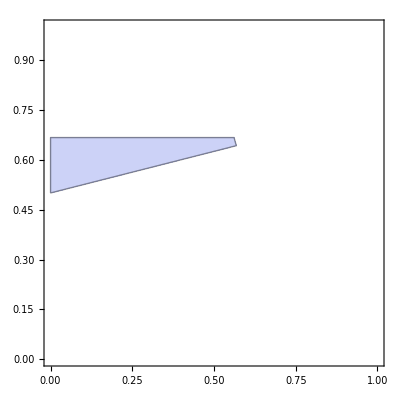

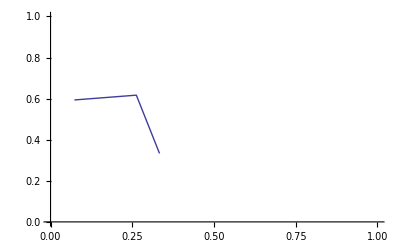

-Graphics-

```mathematica
inp=Import["/Users/astyskin/Documents/workspace/decision/output.txt","Table"];
cons =TakeWhile[inp,#≠{-1}&];
points=Reverse[TakeWhile[Reverse[inp],#≠{-1}&]]
circle[a_,b_]:=Map[(a-#[[2]])^2+(b-#[[3]])^2==#[[1]]^2&,points]
circle[a,b]

RegionPlot[And@@Map[(#.{-1,a,b})>0&,cons],{a,0,1},{b,0,1}]
ListLinePlot[Map[Rest,points],PlotRange->{{0,1},{0,1}}]
ContourPlot[circle[a,b],{a,0,1},{b,0,1}]
```